```mathematica
Clear[H,A,B,x1,x0,psi,out,Dmat,d1,d2,d3,d4,psi0,U,Re0,Re1,Im1,Im0]
Clear[sigX,sigZ,sigY,theta1,theta2,theta3,alpha]
(* Section used for universal objects (pauli's, H, etc.) and functions. If new functions need to be written/tested use a new cell beneath and then merge. 
*)

sigX = PauliMatrix[1];
sigY = PauliMatrix[2];
sigZ = PauliMatrix[3];
H = 1/(Sqrt[2])*{{1,1},{1,-1}};

rz[thetaZ_] := Cos[thetaZ/2]*IdentityMatrix[2] - I*Sin[thetaZ/2]*sigZ;
rx[thetaX_] :=Cos[thetaX/2]*IdentityMatrix[2] - I*Sin[thetaX/2]*sigX;

prod[psi_,phi_]:=( psi.Conjugate[phi])*(phi.Conjugate[psi]);

buildU[alpha_,theta1_,theta2_,theta3_]:= Exp[I*alpha]*rz[theta1].rx[theta2].rz[theta3];
getArgMins[psi_,phi_,params_]:= Module[{Re0,Re1,Im0,Im1},
Re0 = Abs[Re[psi[[1]]] - Re[phi[[1]]]]^2;
Re1 = Abs[Re[psi[[2]]] - Re[phi[[2]]]]^2; 
Im0 = Abs[(Im[psi[[1]]] - Im[phi[[1]]])]^2; 
Im1 = Abs[(Im[psi[[2]]]-  Im[phi[[2]]])]^2;
Return[NArgMin[Re0+Re1+Im0+Im1,params]]
]

getOptDmat[U_,n_] := Module[{A,B,psi,psi0,t,AtU,UtB,Dmat,d1,d2 ,d3,d4,finalMat,phi,temp,tot},
t = {0,0,0,0};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
temp = getArgMins[psi,phi,{d1,d2,d3,d4}];
t = t +temp  ;
];

(* Line below converts a random t to unitary t. *)
t = t/Mean[Abs[t]];
Dmat = DiagonalMatrix[t];
Return[Dmat]
];

testOptMat[Dmat_,U_,n_]:=Module[{A,B,psi,psi0,AtU,UtB,finalMat,phi,results},
results = {};
For[i=0,i<n,i++,
(*Print[StringForm["First For Loop: ``" ,i]];*)
A = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
B = DiagonalMatrix[{Exp[I*RandomReal[{-Pi/2,Pi/2}]],Exp[I*RandomReal[{-Pi/2,Pi/2}]]}];
psi0 = Normalize[RandomComplex[{-1-I,1+I},2]];
psi = B.H.A.psi0;
psi0 = {psi0[[1]],0,psi0[[2]],0};
AtU= ArrayFlatten[TensorProduct[A,U]];
UtB = ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

finalMat = UtB.Dmat.AtU;

phi = finalMat.psi0;
phi = phi[[1;;2]]//Normalize//Simplify;
AppendTo[results,prod[phi,psi]];
];
Return[results]
]


getAverageOverlap[alpha_,theta1_,theta2_,theta3_,n_]:= Module[{U,Dmat,results},
U = buildU[alpha,theta1,theta2,theta3];

Dmat = getOptDmat[U,n];
results = testOptMat[Dmat,U,n];
Return[Mean[results]];
]


getAvgOverlapList[list_,n_]:=getAverageOverlap[list[[1]],list[[2]],list[[3]],list[[4]],n];
h[a_] := getAverageOverlap[Pi/2,a[[1]],a[[2]],Pi/2];

getStdOverlapList[list_,n_]:= Module[{U,Dmat,results},
U = buildU[list[[1]],list[[2]],list[[3]],list[[4]]];

Dmat = getOptDmat[U,n];
results = testOptMat[Dmat,U,n];
Return[StandardDeviation[results]];
]
```

```mathematica
Module[{U,n,Dmat,results},
U = buildU[Pi/2,Pi/2,Pi/2,Pi/2];
n = 100;
Dmat = getOptDmat[U,n];
results=testOptMat[Dmat,U,n];
Print[Dmat];
Print[results];
]
```

{{0.999999,0.,0.,0.},{0.,0.999998,0.,0.},{0.,0.,0.999999,0.},{0.,0.,0.,-1.}}

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ}

```mathematica
2^7
```

128

```mathematica
Clear[dx,dy,ay,by,ax,bx,xAxis,yAxis]
(* Code for Horizontal Section, getting profile of peak along significant axis. 
*)
dx = Pi/(2^8);
ax = Pi/2 -16*dx ;
bx= Pi/2 + 16*dx;

xAxis = AbsoluteTiming[Table[{i,getAvgOverlapList[{Pi/2,i,Pi/2,Pi/2},10]},{i,ax,bx,dx}]];
xAxis2 = AbsoluteTiming[Table[{i,getStdOverlapList[{Pi/2,i,Pi/2,Pi/2},10]},{i,ax,bx,dx}]];
Print[StringForm["Time Elapsed 1: ``",xAxis[[1]]]]

xAxis = xAxis[[2]];
xAxis2 = xAxis2[[2]];
```

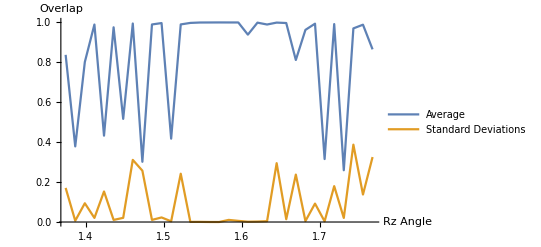

```mathematica
ListPlot[{xAxis,xAxis2},PlotLegends->{"Average","Standard Deviations"},Joined->True,AxesLabel->{"Rz Angle","Overlap"}]
```

```mathematica
Clear[tab0,grid,time,newTab,plotter]
dx = Pi/4;
dy = Pi/4;
ax =Pi/2 -8*dx;
bx = Pi/2 + 8*dx;
ay = Pi/2 -8*dy;
by = Pi/2+8*dy;

tab0 =  Flatten[Table[{Pi/2,i,j,Pi/2},{i,ax,bx,dx},{j,ay,by,dy}],1];
grid =  Flatten[Table[{i,j},{i,ax,bx,dx},{j,ay,by,dy}],1];
time = AbsoluteTiming[Map[getAvgOverlapList,tab0]];
Print[StringForm["Total Time elapsed: ``",time[[1]]]]
newTab = time[[2]];
plotter = Table[Append[grid[[i]],newTab[[i]]],{i,1,Length[grid]}]
```

Total Time elapsed: 76.4346

{{-(3 π)/2,-(3 π)/2,1.+0. ⅈ},{-(3 π)/2,-(5 π)/4,1.+0. ⅈ},{-(3 π)/2,-π,0.395073+0. ⅈ},{-(3 π)/2,-(3 π)/4,1.+0. ⅈ},{-(3 π)/2,-π/2,1.+0. ⅈ},{-(3 π)/2,-π/4,1.+0. ⅈ},{-(3 π)/2,0,0.51256+0. ⅈ},{-(3 π)/2,π/4,1.+0. ⅈ},{-(3 π)/2,π/2,1.+0. ⅈ},{-(3 π)/2,(3 π)/4,1.+0. ⅈ},{-(3 π)/2,π,0.636624+0. ⅈ},{-(3 π)/2,(5 π)/4,1.+0. ⅈ},{-(3 π)/2,(3 π)/2,1.+0. ⅈ},{-(3 π)/2,(7 π)/4,1.+0. ⅈ},{-(3 π)/2,2 π,0.359136+0. ⅈ},{-(3 π)/2,(9 π)/4,1.+0. ⅈ},{-(3 π)/2,(5 π)/2,1.+0. ⅈ},{-(5 π)/4,-(3 π)/2,0.258893+0. ⅈ},{-(5 π)/4,-(5 π)/4,0.543153+0. ⅈ},{-(5 π)/4,-π,0.697307+0. ⅈ},{-(5 π)/4,-(3 π)/4,0.577278+0. ⅈ},{-(5 π)/4,-π/2,0.778001+0. ⅈ},{-(5 π)/4,-π/4,0.417505+0. ⅈ},{-(5 π)/4,0,0.30864+0. ⅈ},{-(5 π)/4,π/4,0.875713+0. ⅈ},{-(5 π)/4,π/2,0.757959+0. ⅈ},{-(5 π)/4,(3 π)/4,0.930561+0. ⅈ},{-(5 π)/4,π,0.732782+0. ⅈ},{-(5 π)/4,(5 π)/4,0.507873+0. ⅈ},{-(5 π)/4,(3 π)/2,0.2773+0. ⅈ},{-(5 π)/4,(7 π)/4,0.300856+0. ⅈ},{-(5 π)/4,2 π,0.446496+0. ⅈ},{-(5 π)/4,(9 π)/4,0.754203+0. ⅈ},{-(5 π)/4,(5 π)/2,0.702975+0. ⅈ},{-π,-(3 π)/2,0.292699+0. ⅈ},{-π,-(5 π)/4,0.444347+0. ⅈ},{-π,-π,0.545577+0. ⅈ},{-π,-(3 π)/4,0.835303+0. ⅈ},{-π,-π/2,0.317452+0. ⅈ},{-π,-π/4,0.664492+0. ⅈ},{-π,0,0.455122+0. ⅈ},{-π,π/4,0.689743+0. ⅈ},{-π,π/2,0.452802+0. ⅈ},{-π,(3 π)/4,0.272637+0. ⅈ},{-π,π,0.569769+0. ⅈ},{-π,(5 π)/4,0.622543+0. ⅈ},{-π,(3 π)/2,0.418551+0. ⅈ},{-π,(7 π)/4,0.268791+0. ⅈ},{-π,2 π,0.606265+0. ⅈ},{-π,(9 π)/4,0.50242+0. ⅈ},{-π,(5 π)/2,0.240881+0. ⅈ},{-(3 π)/4,-(3 π)/2,0.794759+0. ⅈ},{-(3 π)/4,-(5 π)/4,0.708161+0. ⅈ},{-(3 π)/4,-π,0.588296+0. ⅈ},{-(3 π)/4,-(3 π)/4,0.428968+0. ⅈ},{-(3 π)/4,-π/2,0.435102+0. ⅈ},{-(3 π)/4,-π/4,0.550944+0. ⅈ},{-(3 π)/4,0,0.73871+0. ⅈ},{-(3 π)/4,π/4,0.781395+0. ⅈ},{-(3 π)/4,π/2,0.61298+0. ⅈ},{-(3 π)/4,(3 π)/4,0.17997+0. ⅈ},{-(3 π)/4,π,0.335447+0. ⅈ},{-(3 π)/4,(5 π)/4,0.778574+0. ⅈ},{-(3 π)/4,(3 π)/2,0.311933+0. ⅈ},{-(3 π)/4,(7 π)/4,0.56704+0. ⅈ},{-(3 π)/4,2 π,0.42073+0. ⅈ},{-(3 π)/4,(9 π)/4,0.701532+0. ⅈ},{-(3 π)/4,(5 π)/2,0.40259+0. ⅈ},{-π/2,-(3 π)/2,1.+0. ⅈ},{-π/2,-(5 π)/4,1.+0. ⅈ},{-π/2,-π,0.545125+0. ⅈ},{-π/2,-(3 π)/4,1.+0. ⅈ},{-π/2,-π/2,1.+0. ⅈ},{-π/2,-π/4,1.+0. ⅈ},{-π/2,0,0.661627+0. ⅈ},{-π/2,π/4,1.+0. ⅈ},{-π/2,π/2,1.+0. ⅈ},{-π/2,(3 π)/4,1.+0. ⅈ},{-π/2,π,0.64307+0. ⅈ},{-π/2,(5 π)/4,1.+0. ⅈ},{-π/2,(3 π)/2,1.+0. ⅈ},{-π/2,(7 π)/4,1.+0. ⅈ},{-π/2,2 π,0.599206+0. ⅈ},{-π/2,(9 π)/4,1.+0. ⅈ},{-π/2,(5 π)/2,1.+0. ⅈ},{-π/4,-(3 π)/2,0.906192+0. ⅈ},{-π/4,-(5 π)/4,0.651251+0. ⅈ},{-π/4,-π,0.675537+0. ⅈ},{-π/4,-(3 π)/4,0.292438+0. ⅈ},{-π/4,-π/2,0.47028+0. ⅈ},{-π/4,-π/4,0.104346+0. ⅈ},{-π/4,0,0.551455+0. ⅈ},{-π/4,π/4,0.428843+0. ⅈ},{-π/4,π/2,0.272795+0. ⅈ},{-π/4,(3 π)/4,0.367534+0. ⅈ},{-π/4,π,0.302837+0. ⅈ},{-π/4,(5 π)/4,0.580987+0. ⅈ},{-π/4,(3 π)/2,0.665821+0. ⅈ},{-π/4,(7 π)/4,0.653025+0. ⅈ},{-π/4,2 π,0.632736+0. ⅈ},{-π/4,(9 π)/4,0.845158+0. ⅈ},{-π/4,(5 π)/2,0.673555+0. ⅈ},{0,-(3 π)/2,0.638837+0. ⅈ},{0,-(5 π)/4,0.697216+0. ⅈ},{0,-π,0.434232+0. ⅈ},{0,-(3 π)/4,0.471492+0. ⅈ},{0,-π/2,0.396885+0. ⅈ},{0,-π/4,0.560411+0. ⅈ},{0,0,0.596696+0. ⅈ},{0,π/4,0.762416+0. ⅈ},{0,π/2,0.351313+0. ⅈ},{0,(3 π)/4,0.376104+0. ⅈ},{0,π,0.334585+0. ⅈ},{0,(5 π)/4,0.357935+0. ⅈ},{0,(3 π)/2,0.804624+0. ⅈ},{0,(7 π)/4,0.453362+0. ⅈ},{0,2 π,0.207239+0. ⅈ},{0,(9 π)/4,0.45371+0. ⅈ},{0,(5 π)/2,0.50819+0. ⅈ},{π/4,-(3 π)/2,0.422392+0. ⅈ},{π/4,-(5 π)/4,0.510961+0. ⅈ},{π/4,-π,0.747295+0. ⅈ},{π/4,-(3 π)/4,0.897009+0. ⅈ},{π/4,-π/2,0.488712+0. ⅈ},{π/4,-π/4,0.635957+0. ⅈ},{π/4,0,0.59126+0. ⅈ},{π/4,π/4,0.634823+0. ⅈ},{π/4,π/2,0.723327+0. ⅈ},{π/4,(3 π)/4,0.796813+0. ⅈ},{π/4,π,0.320783+0. ⅈ},{π/4,(5 π)/4,0.610322+0. ⅈ},{π/4,(3 π)/2,0.23584+0. ⅈ},{π/4,(7 π)/4,0.719526+0. ⅈ},{π/4,2 π,0.631262+0. ⅈ},{π/4,(9 π)/4,0.324915+0. ⅈ},{π/4,(5 π)/2,0.519915+0. ⅈ},{π/2,-(3 π)/2,1.+0. ⅈ},{π/2,-(5 π)/4,1.+0. ⅈ},{π/2,-π,0.641458+0. ⅈ},{π/2,-(3 π)/4,1.+0. ⅈ},{π/2,-π/2,1.+0. ⅈ},{π/2,-π/4,1.+0. ⅈ},{π/2,0,0.533374+0. ⅈ},{π/2,π/4,1.+0. ⅈ},{π/2,π/2,1.+0. ⅈ},{π/2,(3 π)/4,1.+0. ⅈ},{π/2,π,0.205547+0. ⅈ},{π/2,(5 π)/4,1.+0. ⅈ},{π/2,(3 π)/2,1.+0. ⅈ},{π/2,(7 π)/4,1.+0. ⅈ},{π/2,2 π,0.225795+0. ⅈ},{π/2,(9 π)/4,1.+0. ⅈ},{π/2,(5 π)/2,1.+0. ⅈ},{(3 π)/4,-(3 π)/2,0.352546+0. ⅈ},{(3 π)/4,-(5 π)/4,0.823924+0. ⅈ},{(3 π)/4,-π,0.420514+0. ⅈ},{(3 π)/4,-(3 π)/4,0.446569+0. ⅈ},{(3 π)/4,-π/2,0.672708+0. ⅈ},{(3 π)/4,-π/4,0.790202+0. ⅈ},{(3 π)/4,0,0.484245+0. ⅈ},{(3 π)/4,π/4,0.504981+0. ⅈ},{(3 π)/4,π/2,0.582338+0. ⅈ},{(3 π)/4,(3 π)/4,0.520624+0. ⅈ},{(3 π)/4,π,0.476524+0. ⅈ},{(3 π)/4,(5 π)/4,0.865315+0. ⅈ},{(3 π)/4,(3 π)/2,0.662127+0. ⅈ},{(3 π)/4,(7 π)/4,0.614804+0. ⅈ},{(3 π)/4,2 π,0.384411+0. ⅈ},{(3 π)/4,(9 π)/4,0.587539+0. ⅈ},{(3 π)/4,(5 π)/2,0.422595+0. ⅈ},{π,-(3 π)/2,0.39372+0. ⅈ},{π,-(5 π)/4,0.390783+0. ⅈ},{π,-π,0.809673+0. ⅈ},{π,-(3 π)/4,0.577517+0. ⅈ},{π,-π/2,0.726675+0. ⅈ},{π,-π/4,0.526957+0. ⅈ},{π,0,0.50665+0. ⅈ},{π,π/4,0.622344+0. ⅈ},{π,π/2,0.786308+0. ⅈ},{π,(3 π)/4,0.532733+0. ⅈ},{π,π,0.806246+0. ⅈ},{π,(5 π)/4,0.745619+0. ⅈ},{π,(3 π)/2,0.496522+0. ⅈ},{π,(7 π)/4,0.392063+0. ⅈ},{π,2 π,0.348174+0. ⅈ},{π,(9 π)/4,0.619784+0. ⅈ},{π,(5 π)/2,0.526535+0. ⅈ},{(5 π)/4,-(3 π)/2,0.765207+0. ⅈ},{(5 π)/4,-(5 π)/4,0.604673+0. ⅈ},{(5 π)/4,-π,0.721436+0. ⅈ},{(5 π)/4,-(3 π)/4,0.0584336+0. ⅈ},{(5 π)/4,-π/2,0.203645+0. ⅈ},{(5 π)/4,-π/4,0.886949+0. ⅈ},{(5 π)/4,0,0.448314+0. ⅈ},{(5 π)/4,π/4,0.499414+0. ⅈ},{(5 π)/4,π/2,0.642034+0. ⅈ},{(5 π)/4,(3 π)/4,0.485995+0. ⅈ},{(5 π)/4,π,0.531928+0. ⅈ},{(5 π)/4,(5 π)/4,0.249295+0. ⅈ},{(5 π)/4,(3 π)/2,0.253227+0. ⅈ},{(5 π)/4,(7 π)/4,0.783145+0. ⅈ},{(5 π)/4,2 π,0.558834+0. ⅈ},{(5 π)/4,(9 π)/4,0.524173+0. ⅈ},{(5 π)/4,(5 π)/2,0.273824+0. ⅈ},{(3 π)/2,-(3 π)/2,1.+0. ⅈ},{(3 π)/2,-(5 π)/4,1.+0. ⅈ},{(3 π)/2,-π,0.53078+0. ⅈ},{(3 π)/2,-(3 π)/4,1.+0. ⅈ},{(3 π)/2,-π/2,1.+0. ⅈ},{(3 π)/2,-π/4,1.+0. ⅈ},{(3 π)/2,0,0.663624+0. ⅈ},{(3 π)/2,π/4,1.+0. ⅈ},{(3 π)/2,π/2,1.+0. ⅈ},{(3 π)/2,(3 π)/4,1.+0. ⅈ},{(3 π)/2,π,0.374945+0. ⅈ},{(3 π)/2,(5 π)/4,1.+0. ⅈ},{(3 π)/2,(3 π)/2,1.+0. ⅈ},{(3 π)/2,(7 π)/4,1.+0. ⅈ},{(3 π)/2,2 π,0.620526+0. ⅈ},{(3 π)/2,(9 π)/4,1.+0. ⅈ},{(3 π)/2,(5 π)/2,1.+0. ⅈ},{(7 π)/4,-(3 π)/2,0.226438+0. ⅈ},{(7 π)/4,-(5 π)/4,0.620761+0. ⅈ},{(7 π)/4,-π,0.591135+0. ⅈ},{(7 π)/4,-(3 π)/4,0.639656+0. ⅈ},{(7 π)/4,-π/2,0.605979+0. ⅈ},{(7 π)/4,-π/4,0.113864+0. ⅈ},{(7 π)/4,0,0.304651+0. ⅈ},{(7 π)/4,π/4,0.570588+0. ⅈ},{(7 π)/4,π/2,0.875791+0. ⅈ},{(7 π)/4,(3 π)/4,0.318384+0. ⅈ},{(7 π)/4,π,0.704264+0. ⅈ},{(7 π)/4,(5 π)/4,0.675415+0. ⅈ},{(7 π)/4,(3 π)/2,0.284771+0. ⅈ},{(7 π)/4,(7 π)/4,0.582341+0. ⅈ},{(7 π)/4,2 π,0.269437+0. ⅈ},{(7 π)/4,(9 π)/4,0.350519+0. ⅈ},{(7 π)/4,(5 π)/2,0.492445+0. ⅈ},{2 π,-(3 π)/2,0.13036+0. ⅈ},{2 π,-(5 π)/4,0.863505+0. ⅈ},{2 π,-π,0.612229+0. ⅈ},{2 π,-(3 π)/4,0.498416+0. ⅈ},{2 π,-π/2,0.607528+0. ⅈ},{2 π,-π/4,0.732677+0. ⅈ},{2 π,0,0.561108+0. ⅈ},{2 π,π/4,0.549469+0. ⅈ},{2 π,π/2,0.290097+0. ⅈ},{2 π,(3 π)/4,0.664571+0. ⅈ},{2 π,π,0.519086+0. ⅈ},{2 π,(5 π)/4,0.534089+0. ⅈ},{2 π,(3 π)/2,0.274164+0. ⅈ},{2 π,(7 π)/4,0.44164+0. ⅈ},{2 π,2 π,0.223863+0. ⅈ},{2 π,(9 π)/4,0.273755+0. ⅈ},{2 π,(5 π)/2,0.204592+0. ⅈ},{(9 π)/4,-(3 π)/2,0.755521+0. ⅈ},{(9 π)/4,-(5 π)/4,0.459518+0. ⅈ},{(9 π)/4,-π,0.634897+0. ⅈ},{(9 π)/4,-(3 π)/4,0.954663+0. ⅈ},{(9 π)/4,-π/2,0.338303+0. ⅈ},{(9 π)/4,-π/4,0.698903+0. ⅈ},{(9 π)/4,0,0.547155+0. ⅈ},{(9 π)/4,π/4,0.806799+0. ⅈ},{(9 π)/4,π/2,0.77604+0. ⅈ},{(9 π)/4,(3 π)/4,0.383073+0. ⅈ},{(9 π)/4,π,0.368546+0. ⅈ},{(9 π)/4,(5 π)/4,0.851428+0. ⅈ},{(9 π)/4,(3 π)/2,0.764607+0. ⅈ},{(9 π)/4,(7 π)/4,0.545108+0. ⅈ},{(9 π)/4,2 π,0.548211+0. ⅈ},{(9 π)/4,(9 π)/4,0.804301+0. ⅈ},{(9 π)/4,(5 π)/2,0.184501+0. ⅈ},{(5 π)/2,-(3 π)/2,1.+0. ⅈ},{(5 π)/2,-(5 π)/4,1.+0. ⅈ},{(5 π)/2,-π,0.486602+0. ⅈ},{(5 π)/2,-(3 π)/4,1.+0. ⅈ},{(5 π)/2,-π/2,1.+0. ⅈ},{(5 π)/2,-π/4,1.+0. ⅈ},{(5 π)/2,0,0.7198+0. ⅈ},{(5 π)/2,π/4,1.+0. ⅈ},{(5 π)/2,π/2,1.+0. ⅈ},{(5 π)/2,(3 π)/4,1.+0. ⅈ},{(5 π)/2,π,0.451271+0. ⅈ},{(5 π)/2,(5 π)/4,0.827534+0. ⅈ},{(5 π)/2,(3 π)/2,1.+0. ⅈ},{(5 π)/2,(7 π)/4,1.+0. ⅈ},{(5 π)/2,2 π,0.247552+0. ⅈ},{(5 π)/2,(9 π)/4,1.+0. ⅈ},{(5 π)/2,(5 π)/2,1.+0. ⅈ}}

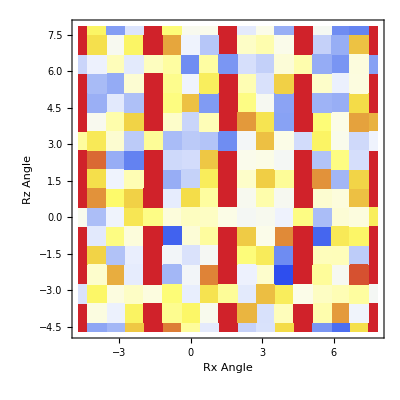

-Graphics3D-

-Graphics3D-

```mathematica
ListDensityPlot[plotter,InterpolationOrder->0,ColorFunction->"TemperatureMap",FrameLabel->{"Rx Angle","Rz Angle"}]
ListPlot3D[{plotter,Flatten[Table[{i,j,0.5},{i,ax,bx,0.1},{j,ay,by,0.1}],1]},InterpolationOrder->10]
```

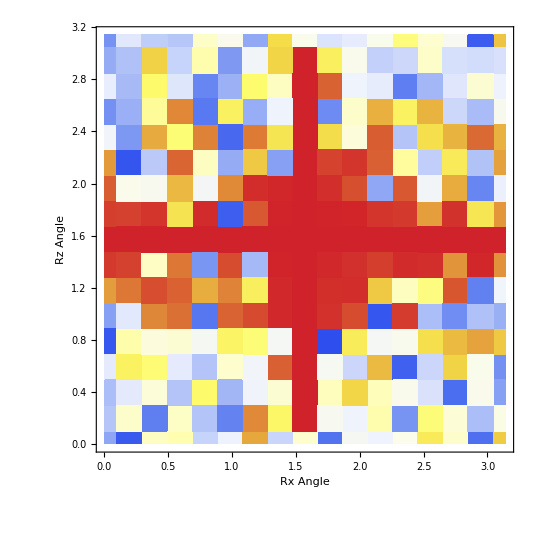

```mathematica
{{1,0},{0,-1}}.{{0,1},{1,0}}
```

{{0,1},{-1,0}}

```mathematica
Clear[alpha,theta1,theta2,theta3,AtU,UtB,Dmat,A,B,a1,a2,b1,b2,psi,psi0,psi1,Dmat,d1,d2,d3,d4]
(* This is Section used for analytic purposes. Idea is to use mathematica to simplify calculations and perform annoying tensor products and matrix calculations symbolically. 
*)
alpha = Pi/2;
theta3 = Pi/2;
U = buildU[alpha,theta1,theta2,theta3]//Simplify;

psi = {psi0,0,psi1,0};

A  = DiagonalMatrix[{a1,a2}];
B = DiagonalMatrix[{b1,b2}];

AtU= ArrayFlatten[TensorProduct[A,U]];
UtB =ArrayFlatten[TensorProduct[ConjugateTranspose[U],B]];

Dmat = DiagonalMatrix[{d1,d2,d3,d4}];
finalMat = UtB.Dmat.AtU.psi//Simplify;

Print["phi"]
phi = FullSimplify[finalMat[[1;;2]],{Element[theta1,Reals],Element[theta2,Reals]}]
Print["psi"]
psi = B.H.A.{psi0,psi1}//Simplify
```

phi

{1/2 b1 (a1 d1 psi0 (1+Cos[theta2])+a2 d3 psi1 (ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2]),1/2 (-a2 b2 d4 psi1 (-1+Cos[theta2])+a1 b2 d2 psi0 (-ⅈ Cos[theta1]+Sin[theta1]) Sin[theta2])}

psi

{(b1 (a1 psi0+a2 psi1))/(√2),(b2 (a1 psi0-a2 psi1))/(√2)}